```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["GeneralUtilities`"]
```

```mathematica
n=12;L=100;
```

```mathematica
scores=ToAssociations[Import["scores.json"]]
```

<|12→<|0.054→<|0.01→<|correct to i for edgeCountDistance greedy→{1.,0.43,0.175,0.075,0.035,0.02,0.01,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},4,correct to i for disagreementCount greedy→{1.,0.505,0.2,0.095,0.05,0.03,0.02,0.01,0.005,0.005,0.005,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}|>,0.02→1|>,6,0.3→1|>,1,25→1|>
 |  |  |  |

```mathematica
scores[["12"]]
```

<|0.054→<|0.01→<|correct to i for edgeCountDistance greedy→{1.,0.43,0.175,0.075,0.035,0.02,0.01,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},4,correct to i for disagreementCount greedy→{1.,0.505,0.2,0.095,0.05,0.03,0.02,0.01,0.005,0.005,0.005,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,36,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}|>,0.02→1|>,6,0.3→1|>
 |  |  |  |

```mathematica
listOfScores = Flatten[With[{nlist = PositionIndex[scores]},Table[With[{plist = PositionIndex[scores[[i]]]},Table[With[{qlist = PositionIndex[scores[[i,j]]]},Table[With[{mlist=PositionIndex[scores[[i,j,k]]]},Table[{nlist[[i,1]],plist[[j,1]],qlist[[k,1]],mlist[[l,1]],scores[[nlist[[i,1]],plist[[j,1]],qlist[[k,1]],mlist[[l,1]]]]},{l,1,Length[mlist]}]],{k,1,Length[qlist]}]],{j,1,Length[plist]}]],{i,1,Length[nlist]}]],3]
```

{{12,0.054,0.01,correct to i for edgeCountDistance greedy,{1.,0.43,0.175,0.075,0.035,0.02,0.01,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},260,{25,3,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,12,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}}
 |  |  |  |

```mathematica
PlotList=ToAssociations[Map[({#[[1]],#[[2]],#[[3]],#[[4]]}->ListPlot[#[[5]]])&,listOfScores]];
```

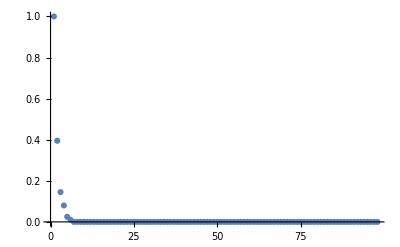

```mathematica
PlotList[{"12","0.1","0.01","correct to i for edgeCountDistance greedy"}]
```

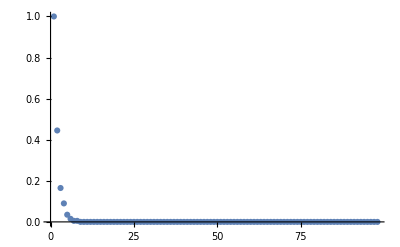

```mathematica
PlotList[{"12","0.1","0.01","correct to i for specDistance greedy"}]
```

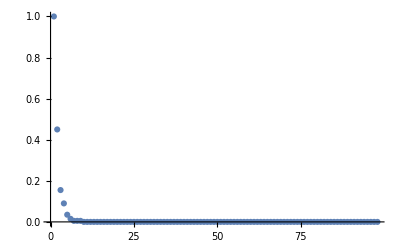

```mathematica
PlotList[{ToString[12],"0.1","0.01","correct to i for doublyStochasticMatrixDistance greedy"}]
```

```mathematica
metricList = {"edgeCountDistance","doublyStochasticMatrixDistance","specDistance","disagreementCount"};plist = {"0.05","0.1","0.2","0.3","0.4","0.5"};qlist = {"0.01", "0.05","0.1","0.2","0.3"};colors={Blue,Red,Green,Purple};
```

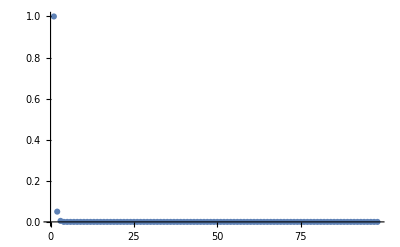

```mathematica
ListPlot[scores["12","0.1","0.2",StringJoin["correct to i for ",metricList[[1]], " greedy"]]]
```

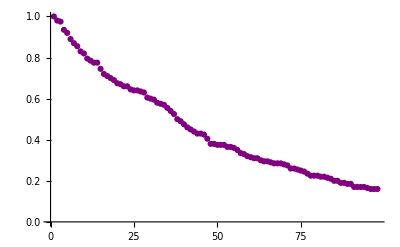

```mathematica
ListPlot[scores["12","0.1","0.2",StringJoin["correct to i for ",metricList[[4]], " greedy"]],PlotStyle->Purple]
```

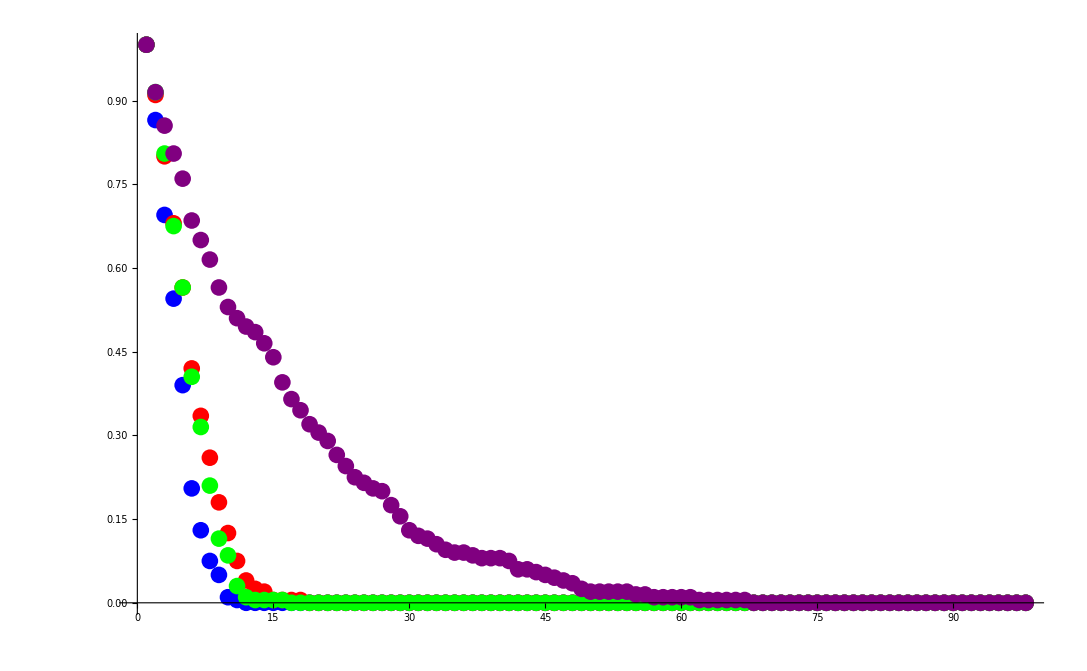

```mathematica
Show[Table[ListPlot[scores["12","0.05","0.05",StringJoin["correct to i for ",metricList[[i]], " greedy"]],PlotStyle->colors[[i]]],{i,1,Length[metricList]}]]
```

```mathematica
FirstPlots = Table[Show[Table[ListLogPlot[Map[(10^-5+#)&,scores["12",plist[[a]],qlist[[b]],StringJoin["correct to i for ",metricList[[i]], " greedy"]]],PlotStyle->colors[[i]],PlotRange->Full],{i,1,Length[metricList]}]],{a,1,Length[plist]},{b,1,Length[qlist]}];
```

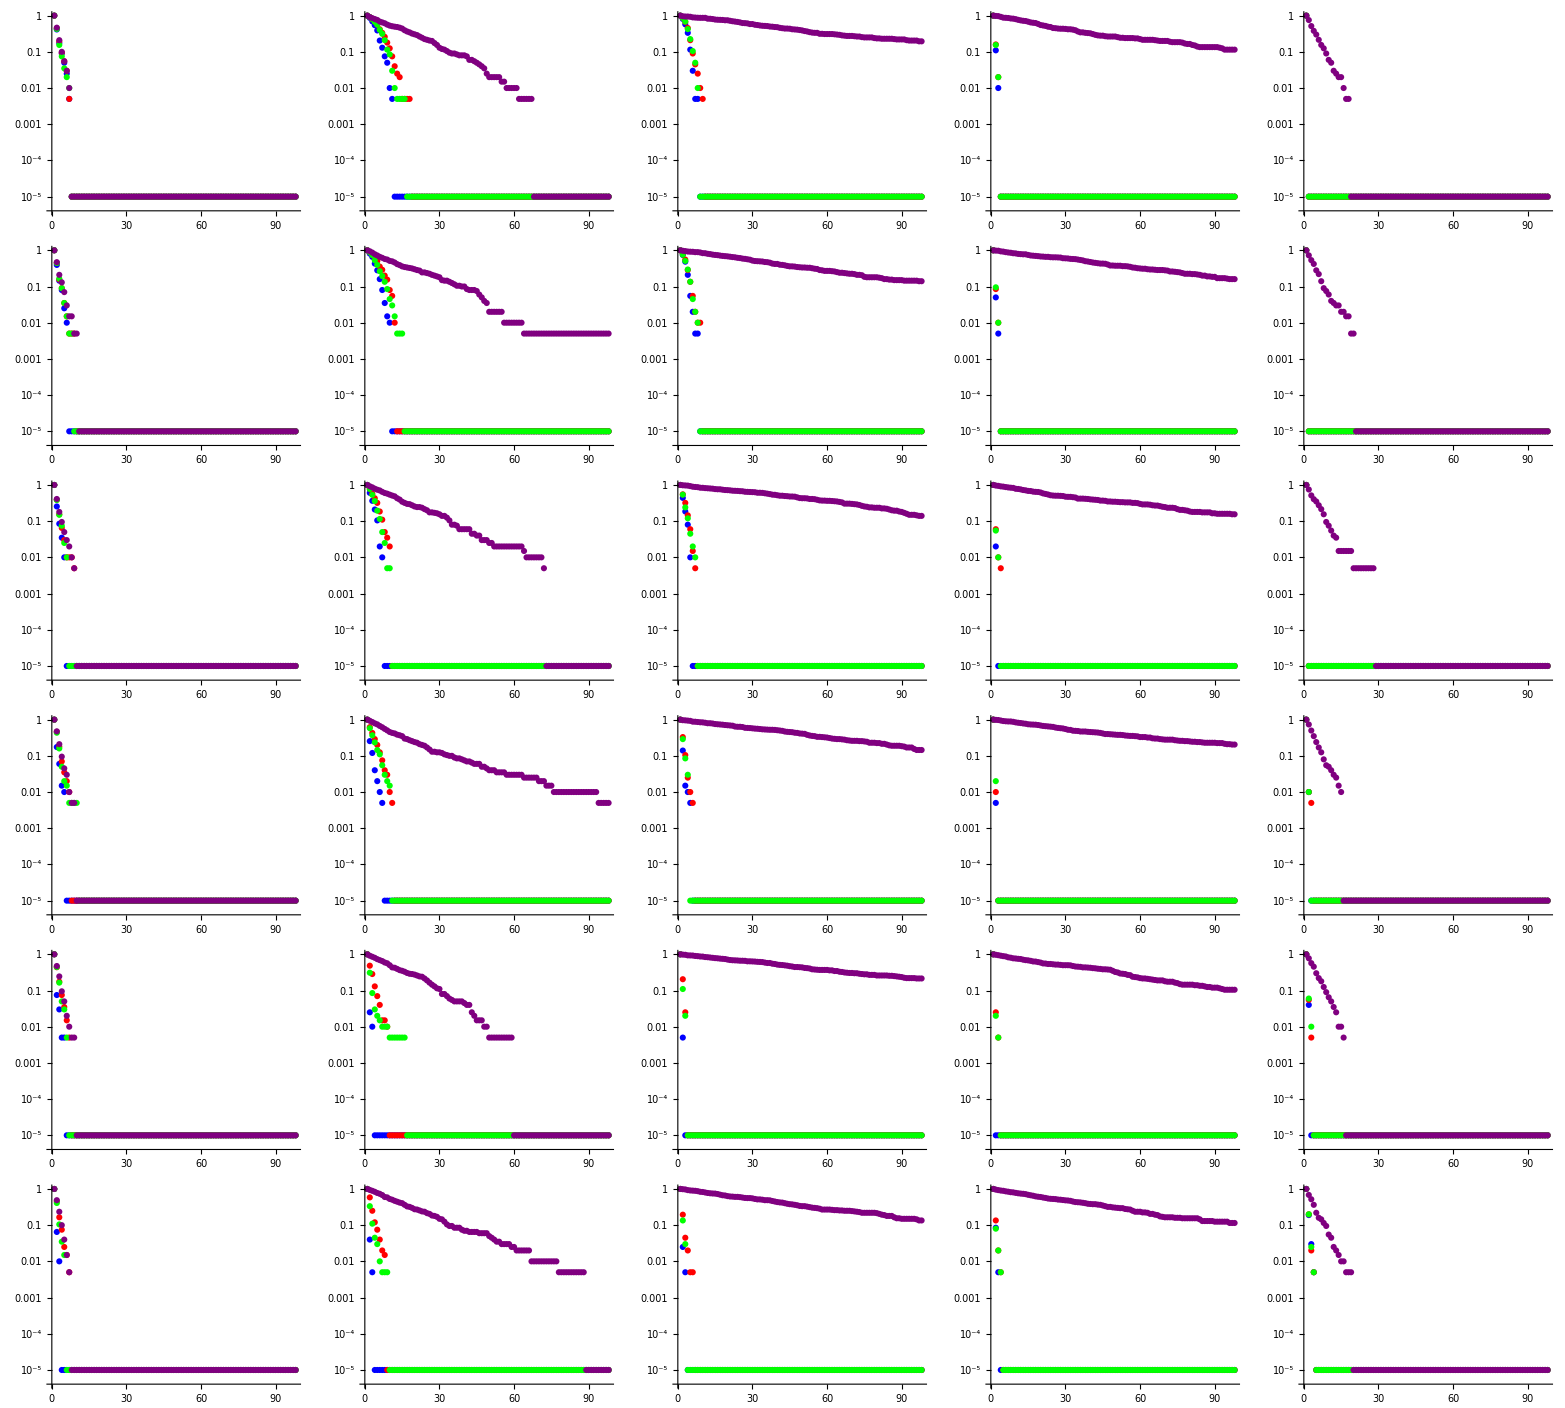
(-Graphics-)

```mathematica
FirstPlots//MatrixForm
```

```mathematica
firstErrorStats=ToAssociations[Import["first_errors.json"]];
```

```mathematica
firstErrorStats[[1]][[1]]
```

<|0.01→<|average first error for disagreementCount greedy→1.925,std of first error for disagreementCount greedy→1.3962,average first error for edgeCountDistance greedy→1.745,std of first error for edgeCountDistance greedy→1.14454,average first error for specDistance greedy→1.795,std of first error for specDistance greedy→1.25418|>,0.02→<|average first error for disagreementCount greedy→3.385,std of first error for disagreementCount greedy→3.03921,average first error for edgeCountDistance greedy→2.265,std of first error for edgeCountDistance greedy→1.57314,average first error for specDistance greedy→2.53,std of first error for specDistance greedy→1.89976|>|>

```mathematica
listOfFES = Flatten[With[{nlist = PositionIndex[firstErrorStats]},Table[With[{plist = PositionIndex[firstErrorStats[[i]]]},Table[With[{qlist = PositionIndex[firstErrorStats[[i,j]]]},Table[With[{mlist=PositionIndex[firstErrorStats[[i,j,k]]]},Table[{nlist[[i,1]],plist[[j,1]],qlist[[k,1]],mlist[[l,1]],firstErrorStats[[nlist[[i,1]],plist[[j,1]],qlist[[k,1]],mlist[[l,1]]]]},{l,1,Length[mlist]}]],{k,1,Length[qlist]}]],{j,1,Length[plist]}]],{i,1,Length[nlist]}]],3];
```

```mathematica
ThirdPlots = Show[Table[ListPlot3D[Flatten[Table[{ToExpression[plist[[a]]],ToExpression[qlist[[b]]],firstErrorStats["12",plist[[a]],qlist[[b]],StringJoin["average first error for ",metricList[[i]], " greedy"]]},{a,1,Length[plist]},{b,1,Length[qlist]}],1],PlotStyle->colors[[i]],PlotRange->All],{i,1,Length[metricList]-1}]]
```

-Graphics3D-

```mathematica
HamRes=Import["HamiltonianResults.mx"]
```

{{1},{{12,0.054,0.01,edgeCountDistance}→{1.645,2.04447},{12,0.054,0.01,specDistance}→{1.825,2.44423},{12,0.054,0.01,disagreementCount}→{2.42,3.1787},{12,0.054,0.02,edgeCountDistance}→{2.86,3.12879},{12,0.054,0.02,specDistance}→{3.725,4.2021},{12,0.054,0.02,disagreementCount}→{6.12,6.36065},124,{10,0.3,0.1,disagreementCount}→{55.19,34.7004},{10,0.3,0.1,specDistance}→{0.33,0.880327},{25,0.12,0.07,edgeCountDistance}→{7.32,2.53768},{25,0.12,0.07,specDistance}→{8.53,2.98558},{25,0.12,0.07,disagreementCount}→{97.,0.},{100,0.035,0.01,edgeCountDistance}→{68.58,12.4296}}}
 |  |  |  |

```mathematica
scoreListHam=ToAssociations[HamRes[[1]]]
```

<|1|>
 |  |  |  |

```mathematica
firstFailureListHam =ToAssociations[HamRes[[2]]]
```

<|{12,0.054,0.01,edgeCountDistance}→{1.645,2.04447},{12,0.054,0.01,specDistance}→{1.825,2.44423},{12,0.054,0.01,disagreementCount}→{2.42,3.1787},{12,0.054,0.02,edgeCountDistance}→{2.86,3.12879},{12,0.054,0.02,specDistance}→{3.725,4.2021},{12,0.054,0.02,disagreementCount}→{6.12,6.36065},{12,0.1,0.05,edgeCountDistance}→{4.235,2.78},{12,0.1,0.05,disagreementCount}→{34.77,28.7216},{12,0.1,0.05,specDistance}→{4.815,3.45113},{12,0.1,0.05,doublyStochasticMatrixDistance}→{5.3,3.69435},{12,0.1,0.01,edgeCountDistance}→{1.735,2.42366},{12,0.1,0.01,disagreementCount}→{2.365,3.0951},{12,0.1,0.01,specDistance}→{1.705,2.41602},{12,0.1,0.01,doublyStochasticMatrixDistance}→{1.7,2.24168},{12,0.1,0.1,edgeCountDistance}→{2.755,1.50208},{12,0.1,0.1,disagreementCount}→{84.02,27.2509},{12,0.1,0.1,specDistance}→{2.845,1.788},{12,0.1,0.1,doublyStochasticMatrixDistance}→{2.955,1.82197},{12,0.1,0.2,edgeCountDistance}→{0.975,0.464168},{12,0.1,0.2,disagreementCount}→{90.935,19.4735},{12,0.1,0.2,specDistance}→{0.855,0.561741},{12,0.1,0.2,doublyStochasticMatrixDistance}→{0.93,0.571606},{12,0.1,0.3,edgeCountDistance}→{0.36,0.481205},{12,0.1,0.3,disagreementCount}→{0.89,3.34422},{12,0.1,0.3,specDistance}→{0.25,0.434099},{12,0.1,0.3,doublyStochasticMatrixDistance}→{0.255,0.436955},{12,0.4,0.05,edgeCountDistance}→{0.105,0.380393},{12,0.4,0.05,disagreementCount}→{33.62,29.3627},{12,0.4,0.05,specDistance}→{0.25,1.0162},{12,0.4,0.05,doublyStochasticMatrixDistance}→{0.38,1.49559},{12,0.4,0.01,edgeCountDistance}→{0.305,0.925341},{12,0.4,0.01,disagreementCount}→{2.325,2.68242},{12,0.4,0.01,specDistance}→{0.655,1.70308},{12,0.4,0.01,doublyStochasticMatrixDistance}→{0.94,2.14696},{12,0.4,0.1,edgeCountDistance}→{0.07,0.274731},{12,0.4,0.1,disagreementCount}→{84.85,26.6808},{12,0.4,0.1,specDistance}→{0.04,0.196451},{12,0.4,0.1,doublyStochasticMatrixDistance}→{0.06,0.277099},{12,0.4,0.2,edgeCountDistance}→{0.055,0.249572},{12,0.4,0.2,disagreementCount}→{87.535,25.9342},{12,0.4,0.2,specDistance}→{0.03,0.171015},{12,0.4,0.2,doublyStochasticMatrixDistance}→{0.035,0.184241},{12,0.4,0.3,edgeCountDistance}→{0.1,0.401004},{12,0.4,0.3,disagreementCount}→{0.78,2.84819},{12,0.4,0.3,specDistance}→{0.065,0.318247},{12,0.4,0.3,doublyStochasticMatrixDistance}→{0.05,0.240393},{12,0.5,0.05,edgeCountDistance}→{0.11,0.434562},{12,0.5,0.05,disagreementCount}→{35.375,30.3168},{12,0.5,0.05,specDistance}→{0.18,0.647841},{12,0.5,0.05,doublyStochasticMatrixDistance}→{0.175,0.841377},{12,0.5,0.01,edgeCountDistance}→{0.22,0.702901},{12,0.5,0.01,disagreementCount}→{2.49,3.0883},{12,0.5,0.01,specDistance}→{0.695,1.5762},{12,0.5,0.01,doublyStochasticMatrixDistance}→{1.06,2.25206},{12,0.5,0.1,edgeCountDistance}→{0.09,0.377641},{12,0.5,0.1,disagreementCount}→{82.22,29.9843},{12,0.5,0.1,specDistance}→{0.075,0.346374},{12,0.5,0.1,doublyStochasticMatrixDistance}→{0.1,0.558174},{12,0.5,0.2,edgeCountDistance}→{0.25,0.607739},{12,0.5,0.2,disagreementCount}→{89.15,23.8814},{12,0.5,0.2,specDistance}→{0.165,0.547057},{12,0.5,0.2,doublyStochasticMatrixDistance}→{0.225,0.637501},{12,0.5,0.3,edgeCountDistance}→{0.46,0.728735},{12,0.5,0.3,disagreementCount}→{1.485,4.50346},{12,0.5,0.3,specDistance}→{0.295,0.624439},{12,0.5,0.3,doublyStochasticMatrixDistance}→{0.345,0.661941},{12,0.05,0.01,edgeCountDistance}→{1.885,2.44164},{12,0.05,0.01,disagreementCount}→{2.51,3.13513},{12,0.05,0.01,specDistance}→{2.08,2.98465},{12,0.05,0.01,doublyStochasticMatrixDistance}→{2.045,2.70733},{12,0.05,0.05,edgeCountDistance}→{4.93,2.63816},{12,0.05,0.05,disagreementCount}→{35.4,28.4773},{12,0.05,0.05,specDistance}→{5.7,3.42031},{12,0.05,0.05,doublyStochasticMatrixDistance}→{5.875,3.85274},{12,0.05,0.1,edgeCountDistance}→{3.22,1.45333},{12,0.05,0.1,disagreementCount}→{84.315,26.2097},{12,0.05,0.1,specDistance}→{3.33,1.71634},{12,0.05,0.1,doublyStochasticMatrixDistance}→{3.45,1.65566},{12,0.05,0.2,edgeCountDistance}→{1.155,0.460473},{12,0.05,0.2,disagreementCount}→{88.02,25.6029},{12,0.05,0.2,specDistance}→{1.085,0.528366},{12,0.05,0.2,doublyStochasticMatrixDistance}→{1.13,0.51422},{12,0.05,0.3,edgeCountDistance}→{0.635,0.482638},{12,0.05,0.3,disagreementCount}→{1.11,3.86687},{12,0.05,0.3,specDistance}→{0.47,0.500352},{12,0.05,0.3,doublyStochasticMatrixDistance}→{0.495,0.50123},{12,0.07,0.03,edgeCountDistance}→{4.095,3.2848},{12,0.07,0.03,disagreementCount}→{13.38,16.4853},{12,0.07,0.03,specDistance}→{4.39,4.20432},{12,0.2,0.01,edgeCountDistance}→{1.47,2.10267},{12,0.2,0.01,disagreementCount}→{2.15,2.99874},{12,0.2,0.01,specDistance}→{1.365,2.12233},{12,0.2,0.01,doublyStochasticMatrixDistance}→{1.555,2.39282},{12,0.2,0.05,edgeCountDistance}→{2.43,1.99877},{12,0.2,0.05,disagreementCount}→{32.035,27.5591},{12,0.2,0.05,specDistance}→{2.815,2.59702},{12,0.2,0.05,doublyStochasticMatrixDistance}→{3.09,2.85},{12,0.2,0.1,edgeCountDistance}→{1.735,1.26601},{12,0.2,0.1,disagreementCount}→{82.185,29.2059},{12,0.2,0.1,specDistance}→{1.59,1.48422},{12,0.2,0.1,doublyStochasticMatrixDistance}→{1.695,1.54073},{12,0.2,0.2,edgeCountDistance}→{0.475,0.557611},{12,0.2,0.2,disagreementCount}→{89.29,23.0282},{12,0.2,0.2,specDistance}→{0.365,0.568676},{12,0.2,0.2,doublyStochasticMatrixDistance}→{0.365,0.602987},{12,0.2,0.3,edgeCountDistance}→{0.075,0.264052},{12,0.2,0.3,disagreementCount}→{1.115,3.78064},{12,0.2,0.3,specDistance}→{0.055,0.228552},{12,0.2,0.3,doublyStochasticMatrixDistance}→{0.045,0.207824},{12,0.3,0.01,edgeCountDistance}→{0.745,1.36723},{12,0.3,0.01,disagreementCount}→{2.66,3.00826},{12,0.3,0.01,specDistance}→{1.315,2.46702},{12,0.3,0.01,doublyStochasticMatrixDistance}→{1.5,2.42889},{12,0.3,0.05,edgeCountDistance}→{1.025,1.59597},{12,0.3,0.05,disagreementCount}→{36.41,30.8518},{12,0.3,0.05,specDistance}→{1.425,2.50915},{12,0.3,0.05,doublyStochasticMatrixDistance}→{1.465,2.61399},{12,0.3,0.1,edgeCountDistance}→{0.685,0.859926},{12,0.3,0.1,disagreementCount}→{82.43,28.8581},{12,0.3,0.1,specDistance}→{0.5,0.868199},{12,0.3,0.1,doublyStochasticMatrixDistance}→{0.605,1.08853},{12,0.3,0.2,edgeCountDistance}→{0.11,0.313675},{12,0.3,0.2,disagreementCount}→{88.715,23.3454},{12,0.3,0.2,specDistance}→{0.05,0.240393},{12,0.3,0.2,doublyStochasticMatrixDistance}→{0.08,0.289862},{12,0.3,0.3,edgeCountDistance}→{0.02,0.172478},{12,0.3,0.3,disagreementCount}→{1.08,3.38985},{12,0.3,0.3,specDistance}→{0.03,0.222141},{12,0.3,0.3,doublyStochasticMatrixDistance}→{0.02,0.223269},{10,0.3,0.1,edgeCountDistance}→{0.4,0.83876},{10,0.3,0.1,disagreementCount}→{55.19,34.7004},{10,0.3,0.1,specDistance}→{0.33,0.880327},{25,0.12,0.07,edgeCountDistance}→{7.32,2.53768},{25,0.12,0.07,specDistance}→{8.53,2.98558},{25,0.12,0.07,disagreementCount}→{97.,0.},{100,0.035,0.01,edgeCountDistance}→{68.58,12.4296}|>

```mathematica
listOfFESHam=With[{keyList = PositionIndex[firstFailureListHam]},Table[Join[keyList[[i,1]],firstFailureListHam[keyList[[i,1]]]],{i,1,Length[keyList]}]];
```

```mathematica
listOfFESHam[[1]]
```

{12,0.054,0.01,edgeCountDistance,1.645,2.04447}

```mathematica
ThirdPlotsHam =Show[ Table[ListPlot3D[Flatten[Table[{ToExpression[plist[[a]]],ToExpression[qlist[[b]]],firstFailureListHam[{"12",plist[[a]],qlist[[b]],metricList[[i]]}][[1]]},{a,1,Length[plist]},{b,1,Length[qlist]}],1],PlotStyle->colors[[i]],PlotRange->All],{i,1,Length[metricList]-1}]]
```

-Graphics3D-